# e^-e^+→e^-e^+

## Feynman Diagram



```mathematica
R1=CreateTopologies[0, 2 -> 2];
Paint[%];
```

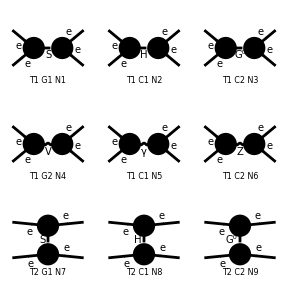

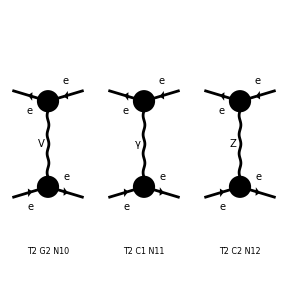

```mathematica
S1=CreateTopologies[0, 2 -> 2];Diagrams=InsertFields[R1,{-F[2,{1}],F[2,{1}]}->{-F[2,{1}],F[2,{1}]}];
Paint[%];
```

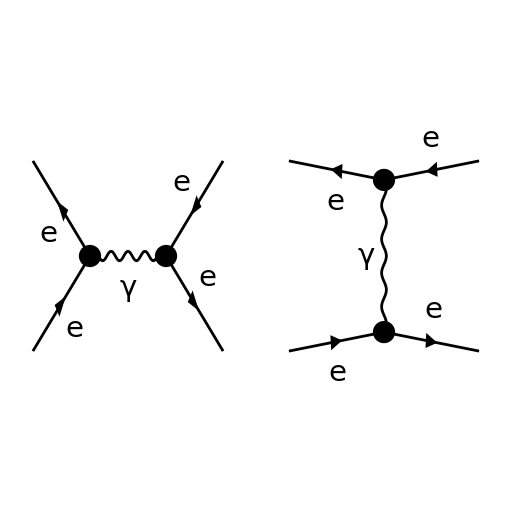

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diags1 = InsertFields[T1, {-F[2, {1}], F[2, {1}]} ->
		{-F[2, {1}], F[2, {1}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diags1, ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

## Square amplitude (Momenta)

```mathematica
A = FCFAConvert[CreateFeynAmp[diags1, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(OverBar[k'],m_e)).(ⅈ e (γ̄)^Lor2).(φ(-k̄,m_e)) (φ(-p̄,m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p'],m_e)))/(OverBar[k']+k̄)^2-((ḡ)^Lor1Lor2 (φ(-p̄,m_e)).(ⅈ e (γ̄)^Lor1).(φ(-k̄,m_e)) (φ(OverBar[k'],m_e)).(ⅈ e (γ̄)^Lor2).(φ(OverBar[p'],m_e)))/(OverBar[k']-OverBar[p'])^2

```mathematica
ComplexConjugate[A]
```

(e^2 (ḡ)^Lor1Lor2 (φ(-k̄,m_e)).(γ̄)^Lor1.(φ(-p̄,m_e)) (φ(OverBar[p'],m_e)).(γ̄)^Lor2.(φ(OverBar[k'],m_e)))/(OverBar[k']-OverBar[p'])^2-(e^2 (ḡ)^Lor1Lor2 (φ(-k̄,m_e)).(γ̄)^Lor2.(φ(OverBar[k'],m_e)) (φ(OverBar[p'],m_e)).(γ̄)^Lor1.(φ(-p̄,m_e)))/(OverBar[k']+k̄)^2

```mathematica
sqAmp =ChangeDimension[(A (ComplexConjugate[A]//FCRenameDummyIndices))//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify, D]
```

8 e^4 ((1/(k'+k)^2)^2 (m_e^2 (k·k'+p·p')+2 m_e^4+(k·p') (p·k')+(k·p) (k'·p'))+(m_e^2 (2 m_e^2-k'·p'+p·k'+k·k'-k·p+p·p')+(k·p') (m_e^2+2 (p·k')))/((k'+k)^2 (k'-p')^2)+(1/(k'-p')^2)^2 (-m_e^2 (k'·p'+k·p)+2 m_e^4+(k·p') (p·k')+(k·k') (p·p')))

```mathematica
masslessElectronssqAmp= (sqAmp/. {SMP["m_e"] -> 0}/.{Momentum[k,D]+Momentum[k',D]->q}/.{Momentum[k',D]-Momentum[p',D]->q'})//FullSimplify
```

8 e^4 ((1/q^2)^2 ((k·p') (p·k')+(k·p) (k'·p'))+(1/(q')^2)^2 ((k·p') (p·k')+(k·k') (p·p'))+(2 (k·p') (p·k'))/(q^2 (q')^2))

```mathematica
q=(FVD[k',μ]-FVD[p',μ])^2//Expand2//Contract
```

-2 (k'·p')+k'^2+p'^2

```mathematica
q=.
```

## Kinematics

Diagram 1

Incoming Momenta - p (electron), p’(positron)

p^μ=(p^0,p^1,p^2,p^3)
p_e=(E_e, 0, 0, p_e z )
p'_p=(E_p, 0, 0, -p_pz )
Invariant: p_e^2=E_e^2-m_e^2

Outgoing Momenta - k (electron), k’ (positron)

k^μ=(k^0,k^1,k^2,k^3)
k_e=(E_e, k_e x, k_e y, k_e z )=(E_e, k )
k'_p=(E_p, -k_px, -k_py,- k_pz )=(E_p, -k )
Invariant: k_p^2=E_p^2-m_p^2

General:
s = ( p^μ+p'^μ )^2 =( k^μ+k'^μ )^2 = (p)^2+(p')^2+2( p*p' ) = (p^0)^2-p^2+(p'^0)^2-p'^2+2 p^0 p'^0-2p p'cos( θ ) = 

t = ( k^μ-p^μ )^2 = ( k'^μ-p'^μ )^2 = (k)^2+(p)^2-2( k*p ) = (k^0)^2-k^2+(p^0)^2-p^2-2 k^0 p^0+2k p cos( θ )

u = ( k'^μ-p^μ )^2 = ( k^μ-p'^μ )^2 = (k')^2+(p)^2+2( k'*p ) = (k'^0)^2-k'^2+(p^0)^2-p^2-2 k'^0 p^0+2k' p cos( θ )

```mathematica
Inputs
```

Inputs

```mathematica
p10=Ee;
p11=0;
p12=0;
p13=Subscript[p, e];
pp10=Ep;
pp11=0;
pp12=0;
pp13=-Subscript[p, p];
k10=Ee;
k11=kx;
k12=ky;
k13=kz;
kp10=Ep;
kp11=-kx;
kp12=-ky;
kp13=-kz;
θz=0;
θ=θ;
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
pdotpp1=Inner[Times,{p10,p11,p12,p13},Inner[Times,g,{pp10,pp11,pp12,pp13},Plus],Plus]
kdotkp1=Inner[Times,{k10,k11,k12,k13},Inner[Times,g,{kp10,kp11,kp12,kp13},Plus],Plus]
kdotp1=Inner[Times,{k10,k11,k12,k13},Inner[Times,g,{p10,p11,p12,p13},Plus], Plus]
kpdotpp1=Inner[Times,{kp10,kp11,kp12,kp13},Inner[Times,g,{pp10,pp11,pp12,pp13},Plus],Plus]
kpdotp1=Inner[Times,{kp10,kp11,kp12,kp13},Inner[Times,g,{p10,p11,p12,p13},Plus],Plus]
kdotpp1=Inner[Times,{k10,k11,k12,k13},Inner[Times,g,{pp10,pp11,pp12,pp13},Plus],Plus]
zhat=cos[θ]
```

p_p p_e+Ee Ep

Ee Ep+kx^2+ky^2+kz^2

Ee^2-kz p_e

Ep^2-kz p_p

kz p_e+Ee Ep

Ee Ep+kz p_p

cos(θ)

```mathematica
mass1=0;
mass2=Subscript[m, p];
E1=Ee;
E2=Ep;
E3=Ee;
E4=Ep;

Subscript[p, e]=√(E1^2-mass1^2)//PowerExpand;
Subscript[k, p]=√(E2^2-mass2^2)//PowerExpand;
|p|=√(E3^2-mass1^2)//PowerExpand;
|k|=√(E4^2-mass2^2)//PowerExpand;
|p'|=-|p|;
|k'|=-|k|;
kz=|k|zhat;
kz=.
```

```mathematica
pdotpp1
kdotp1
kpdotp1
```

Ee Ep+Ee p_p

Ee^2-Ee kz

Ee Ep+Ee kz

```mathematica
schannel1=p10^2-(|p|)^2+pp10^2-(|p'|)^2+2*p10*pp10-2*|p|*|p'|*Cos[θz]

tchannel1=k10^2-(|k|)^2+p10^2-(|p|)^2-2*k10*p10+2*|k|*|p|*Cos[θ]

uchannel1=kp10^2-(|k'|)^2+p10^2-(|p|)^2-2*kp10*p10+2*|k'|*|p|*Cos[θ]
```

Ee^2+2 Ee Ep+Ep^2

-Ee^2+2 Ee cos(θ) √(Ep^2-m_p^2)-Ep^2+m_p^2

-2 Ee cos(θ) √(Ep^2-m_p^2)-2 Ee Ep+m_p^2

Diagram 2

Incoming Momenta - p (electron), p’(positron)

p^μ=(p^0,p^1,p^2,p^3)
p_e=(E_e, 0, 0, p_e z )
p'_p=(E_p, 0, 0, -p_pz )
Invariant: p_e^2=E_e^2-m_e^2

Outgoing Momenta - k (electron), k’ (positron)

k^μ=(k^0,k^1,k^2,k^3)
k_e=(E_e, k_e x, k_e y, k_e z )=(E_e, k )
k'_p=(E_p, -k_px, -k_py,- k_pz )=(E_p, -k )
Invariant: k_μ^2=E_μ^2-m_μ^2

```mathematica
Inputs
```

Inputs

```mathematica
p20=Ee;
p21=0;
p22=0;
p23=Subscript[p, e];
pp20=Ee;
pp21=0;
pp22=0;
pp23=-Subscript[p, p];
k20=Ep;
k21=kx;
k22=ky;
k23=kz;
kp20=Ep;
kp21=-kx;
kp22=-ky;
kp23=-kz;
θz=0;
θ=θ;
```

```mathematica
pdotpp2=Inner[Times,{p20,p21,p22,p23},Inner[Times,g,{pp20,pp21,pp22,pp23},Plus],Plus]
kdotkp2=Inner[Times,{k20,k21,k22,k23},Inner[Times,g,{kp20,kp21,kp22,kp23},Plus],Plus]
kdotp2=Inner[Times,{k20,k21,k22,k23},Inner[Times,g,{p20,p21,p22,p23},Plus], Plus]
kpdotpp2=Inner[Times,{kp20,kp21,kp22,kp23},Inner[Times,g,{pp20,pp21,pp22,pp23},Plus],Plus]
kpdotp2=Inner[Times,{kp20,kp21,kp22,kp23},Inner[Times,g,{p20,p21,p22,p23},Plus],Plus]
kdotpp2=Inner[Times,{k20,k21,k22,k23},Inner[Times,g,{pp20,pp21,pp22,pp23},Plus],Plus]
zhat=cos[θ]
```

Ee^2+Ee p_p

Ep^2+kx^2+ky^2+kz^2

Ee Ep-Ee kz

Ee Ep-kz p_p

Ee Ep+Ee kz

Ee Ep+kz p_p

cos(θ)

```mathematica
mass1=0;
mass2=Subscript[m, p];
E1=Ee;
E2=Ep;
E3=Ee;
E4=Ep;

Subscript[p, e]=√(E1^2-mass1^2)//PowerExpand;
Subscript[p, p]=√(E2^2-mass2^2)//PowerExpand;
|p|=√(E3^2-mass1^2)//PowerExpand;
|k|=√(E4^2-mass2^2)//PowerExpand;
|p'|=-|p|;
|k'|=-|k|;
```

```mathematica
schannel2=p20^2-(|p|)^2+pp20^2-(|p'|)^2+2*p20*pp20-2*|p|*|p'|*Cos[θz]

tchannel2=k20^2-(|k|)^2+p20^2-(|p|)^2-2*k20*p20+2*|k|*|p|*Cos[θ]

uchannel2=kp20^2-(|k'|)^2+p20^2-(|p|)^2-2*kp20*p20+2*|k'|*|p|*Cos[θ]
```

4 Ee^2

2 Ee cos(θ) √(Ep^2-m_p^2)-2 Ee Ep+m_p^2

-2 Ee cos(θ) √(Ep^2-m_p^2)-2 Ee Ep+m_p^2

```mathematica
Ee=Subscript[p, p]=k;
```

```mathematica
pdotpp2//Factor1
kdotpp2//Factor1
kdotp2//Factor1
-2*kdotp2//Factor1
```

2 k^2

k (Ep+kz)

k (Ep-kz)

-2 k (Ep-kz)

```mathematica
kz=Ee Cos[θ]
```

k cos(θ)

```mathematica
pdotpp2//Factor1
kdotpp2//Factor1
kdotp2//Factor1
-2*kdotp2//Factor1
```

2 k^2

k (Ep+k cos(θ))

k (Ep-k cos(θ))

-2 k (Ep-k cos(θ))

```mathematica
schannel1
schannel2
tchannel1
tchannel2
```

Ep^2+2 Ep k+k^2

4 k^2

2 k cos(θ) √(Ep^2-m_p^2)-Ep^2-k^2+m_p^2

2 k cos(θ) √(Ep^2-m_p^2)-2 Ep k+m_p^2

```mathematica
schannel1==schannel2
tchannel1==tchannel2
```

Ep^2+2 Ep k+k^2==4 k^2

2 k cos(θ) √(Ep^2-m_p^2)-Ep^2-k^2+m_p^2==2 k cos(θ) √(Ep^2-m_p^2)-2 Ep k+m_p^2

```mathematica
schannel3=4 Eg^2
tchannel3=-2 k^2(1-Cos[θ])
```

4 Eg^2

-2 k^2 (1-cos(θ))

## Cross Section

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EB=Ecm/2;
EA=|p|;
SPD[p,k]= kdotp2;
SPD[p,k']= kdotpp2;
SPD[p,p']=(schannel3)/2;
SPD[p',k']=SPD[p,k];
SPD[p',k]=SPD[p,k'];
SPD[k,k']=SPD[p,p'];
q=(schannel3)^(1/2);
q'=(tchannel3)^(1/2);
```

```mathematica
q^4
(q')^4
```

16 Eg^4

4 k^4 (1-cos(θ))^2

```mathematica
masslessElectronssqAmp
```

8 e^4 ((-1/(2 k^2 (1-cos(θ))))^2 (4 Eg^4+(Ep k+k^2 cos(θ))^2)-((Ep k+k^2 cos(θ))^2)/(4 Eg^2 k^2 (1-cos(θ)))+(1/(4 Eg^2))^2 ((Ep k-k^2 cos(θ))^2+(Ep k+k^2 cos(θ))^2))

```mathematica
Ep=k;
```

```mathematica
masslessElectronssqAmp
```

8 e^4 ((-1/(2 k^2 (1-cos(θ))))^2 (4 Eg^4+(k^2 cos(θ)+k^2)^2)-((k^2 cos(θ)+k^2)^2)/(4 Eg^2 k^2 (1-cos(θ)))+(1/(4 Eg^2))^2 ((k^2-k^2 cos(θ))^2+(k^2 cos(θ)+k^2)^2))

```mathematica
(k^2-k^2 Cos[θ])^2//Factor1
(k^2+k^2 Cos[θ])^2//Factor1
```

k^4 (1-cos(θ))^2

k^4 (cos(θ)+1)^2

```mathematica
Test=8 e^4((1/q^4*(k^2-k^2 Cos[θ])^2//Factor1)+1/q^4*((k^2+k^2 Cos[θ])^2//Factor1)+2/(q^2*(q')^2)((k^2+k^2 Cos[θ])^2//Factor1)+1/q'^4*(4 Eg^4+((k^2+k^2 Cos[θ])^2//Factor1)))
```

8 e^4 ((k^4 (1-cos(θ))^2)/(16 Eg^4)+(k^4 (cos(θ)+1)^2)/(16 Eg^4)+(4 Eg^4+k^4 (cos(θ)+1)^2)/(4 k^4 (1-cos(θ))^2)-(k^2 (cos(θ)+1)^2)/(4 Eg^2 (1-cos(θ))))

```mathematica
Test=8 e^4*1/4(Distribute[4*((1/q^4*(k^2-k^2 Cos[θ])^2//Factor1)+1/q^4*((k^2+k^2 Cos[θ])^2//Factor1)+2/(q^2*(q')^2)((k^2+k^2 Cos[θ])^2//Factor1)+1/q'^4*(4 Eg^4+((k^2+k^2 Cos[θ])^2//Factor1)))])
```

2 e^4 ((k^4 (1-cos(θ))^2)/(4 Eg^4)+(k^4 (cos(θ)+1)^2)/(4 Eg^4)+(4 Eg^4+k^4 (cos(θ)+1)^2)/(k^4 (1-cos(θ))^2)-(k^2 (cos(θ)+1)^2)/(Eg^2 (1-cos(θ))))

```mathematica
Collect[Test,(Cos[θ]+1)]
```

2 e^4 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4))+2 e^4 (cos(θ)+1)^2 (k^4/(4 Eg^4)-k^2/(Eg^2 (1-cos(θ)))+1/(1-cos(θ))^2)

```mathematica
Collect[%,2 e^4]
```

2 e^4 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+(cos(θ)+1)^2 (k^4/(4 Eg^4)-k^2/(Eg^2 (1-cos(θ)))+1/(1-cos(θ))^2))

```mathematica
Test=2 e^4((4 Eg^4)/(k^4(1-Cos[θ])^2)+(k^4(1-Cos[θ])^2)/(4 Eg^4)+k^4(1+Cos[θ])^2(Distribute[1/k^4*(k^4/(4 Eg^4)-k^2/(Eg^2(1-Cos[θ]))+1/(1-Cos[θ])^2)]))
```

2 e^4 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+k^4 (cos(θ)+1)^2 (1/(4 Eg^4)-1/(Eg^2 k^2 (1-cos(θ)))+1/(k^4 (1-cos(θ))^2)))

```mathematica
(1/((2 Eg^2)^2)-2/(2 Eg^2 k^2(1-Cos[θ]))+1/((k^2(1-Cos[θ]))^2))==(1/(2 Eg^2)-1/(k^2(1-Cos[θ])))^2
```

1/(4 Eg^4)-1/(Eg^2 k^2 (1-cos(θ)))+1/(k^4 (1-cos(θ))^2)==(1/(2 Eg^2)-1/(k^2 (1-cos(θ))))^2

```mathematica
Msq=2 e^4((4 Eg^4)/(k^4(1-Cos[θ])^2)+(k^4(1-Cos[θ])^2)/(4 Eg^4)+k^4(1+Cos[θ])^2(1/(2 Eg^2)-1/(k^2(1-Cos[θ])))^2)
```

2 e^4 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+k^4 (cos(θ)+1)^2 (1/(2 Eg^2)-1/(k^2 (1-cos(θ))))^2)

```mathematica
Sigma=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|p|)/(4 π^2 4Ecm)*Msq
```

(dϕ e^4 d(Cos θ) ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+k^4 (cos(θ)+1)^2 (1/(2 Eg^2)-1/(k^2 (1-cos(θ))))^2))/(32 π^2 Ecm^2)

```mathematica
dϕ=2π;
Sigma/d[Cos θ]
```

(e^4 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+k^4 (cos(θ)+1)^2 (1/(2 Eg^2)-1/(k^2 (1-cos(θ))))^2))/(16 π Ecm^2)

```mathematica
e=√(4π α);
Ecm=(4 Eg^2)^(1/2);
dσ/(d cos[θ])==Sigma/d[Cos θ]
```

dσ/(d cos(θ))==(π α^2 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+k^4 (cos(θ)+1)^2 (1/(2 Eg^2)-1/(k^2 (1-cos(θ))))^2))/(4 Eg^2)

## Square Amplitude (Mandelstam)

```mathematica
B = FCFAConvert[CreateFeynAmp[diags1, Truncated -> False],
IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(OverBar[k2],m_e)).(ⅈ e (γ̄)^Lor2).(φ(-OverBar[k1],m_e)) (φ(-OverBar[p1],m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p2],m_e)))/(OverBar[k1]+OverBar[k2])^2-((ḡ)^Lor1Lor2 (φ(-OverBar[p1],m_e)).(ⅈ e (γ̄)^Lor1).(φ(-OverBar[k1],m_e)) (φ(OverBar[k2],m_e)).(ⅈ e (γ̄)^Lor2).(φ(OverBar[p2],m_e)))/(OverBar[k2]-OverBar[p2])^2

```mathematica
SetMandelstam[s, t, u, p1, p2, -k1, -k2, SMP["m_e"], SMP["m_e"], SMP["m_e"], SMP["m_e"]];
sqAmpM =(B (ComplexConjugate[B]//FCRenameDummyIndices))//PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (8 m_e^4 (s^2+s t+t^2)-4 m_e^2 (s^3+s^2 (u-2 t)+s t (3 u-2 t)+t^2 (t+u))+s^4+s^2 u^2+2 s t u^2+t^4+t^2 u^2))/(s^2 t^2)

```mathematica
masslessElectronssqAmpmandel= (sqAmpM/. {SMP["m_e"] -> 0})//FullSimplify
```

(2 e^4 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
SqampMandel=(2 e^4)((u^2(Simplify[(s+t)/(s t)])^2)+(s^4/(s^2 t^2)+t^4/(s^2 t^2)))
```

32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

```mathematica
e=√(4π α);
```

```mathematica
SqampMandel
```

32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

```mathematica
s=4 Eg^2;
t=-2 k^2(1-Cos[θ]);
u=-2 k^2(1+Cos[θ]);
```

```mathematica
SqampMandel
```

32 π^2 α^2 ((4 Eg^4)/(k^4 (1-cos(θ))^2)+(k^4 (1-cos(θ))^2)/(4 Eg^4)+4 k^4 (cos(θ)+1)^2 (1/(4 Eg^2)-1/(2 k^2 (1-cos(θ))))^2)

```mathematica
Clear[s,t,u]
```

```mathematica
SqampMandel
```

32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

## Cross Section (Mandelstam)

```mathematica
Clear[Ecm]
```

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EB=Ecm/2;
EA=|p|;
SPD[p,k]= kdotp2;
SPD[p,k']= kdotpp2;
SPD[p,p']=(schannel3)/2;
SPD[p',k']=SPD[p,k];
SPD[p',k]=SPD[p,k'];
SPD[k,k']=SPD[p,p'];
q=(schannel3)^(1/2);
q'=(tchannel3)^(1/2);
dϕ=2π;
SigmaM=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|p|)/(4 π^2 4Ecm)*SqampMandel
```

(π α^2 d(Cos θ) (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2))/Ecm^2

```mathematica
Ecm=(s)^(1/2);
dσ/(d cos[θ])==SigmaM/d[Cos θ]
```

dσ/(d cos(θ))==(π α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2))/s

## Plot (Mandelstam Cross Section)

```mathematica
SigmaM/d[Cos θ]
```

(π α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2))/s

```mathematica
2/s*dσ/(2/s*dt)==2/s*SigmaM/d[Cos θ]
```

dσ/dt==(2 π α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2))/s^2

```mathematica
BhabhaCross=1/x^2*(x^2/z^2+z^2/x^2+y^2(1/x+1/z)^2)
```

(x^2/z^2+z^2/x^2+y^2 (1/x+1/z)^2)/x^2

```mathematica
Plot[BhabhaCross,{z,0,1}]
```

-Graphics-

```mathematica
BhabhaCross//Expand
```

y^2/x^4+z^2/x^4+(2 y^2)/(x^3 z)+y^2/(x^2 z^2)+1/z^2

```mathematica
Combine[x^2/z^2+z^2/x^2+y^2(1/x+1/z)^2]
```

(x^4+x^2 y^2+2 x y^2 z+y^2 z^2+z^4)/(x^2 z^2)

```mathematica
Plot[%,{z,0,1}]
```

-Graphics-

```mathematica
Numerator[%%%%]
```

x^4+x^2 y^2+2 x y^2 z+y^2 z^2+z^4

```mathematica
(x^2+y^2)(x^2+z^2)//Expand
```

x^4+x^2 y^2+x^2 z^2+y^2 z^2

## Scratch

```mathematica
New=(masslessElectronssqAmpmandel/.{e=√(4π α)})//FullSimplify
```

ReplaceAll::reps: {2 √π √α} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 e^4 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)/.{2 √π √α}

```mathematica
masslessElectronssqAmpmandel*(s^2 t^2)/(2*e^4)//Expand
```

(e^4 s^4)/e^4+(e^4 s^2 u^2)/e^4+(2 e^4 s t u^2)/e^4+(e^4 t^4)/e^4+(e^4 t^2 u^2)/e^4

```mathematica
FullSimplify[%]
```

(e^4 (s^4+u^2 (s+t)^2+t^4))/e^4

```mathematica
Cancel[(e^4(s^4+u^2 (s+t)^2+t^4))/e^4]*Distribute[1/(s^2 t^2)]//Expand
```

s^2/t^2+t^2/s^2+u^2/s^2+(2 u^2)/(s t)+u^2/t^2

```mathematica
Collect[%,s]
```

(t^2+u^2)/s^2+s^2/t^2+(2 u^2)/(s t)+u^2/t^2

```mathematica
sqAmpAtest= (A (ComplexConjugate[A]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract
```

(16 e^4 m_e^4)/((-2 (OverBar[k']·OverBar[p'])+OverBar[k']^2+OverBar[p']^2)^2)+(8 e^4 m_e^2 (p̄·OverBar[p']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)-(8 e^4 m_e^2 (k̄·p̄))/((-2 (OverBar[k']·OverBar[p'])+OverBar[k']^2+OverBar[p']^2)^2)-(8 e^4 m_e^2 (OverBar[k']·OverBar[p']))/((-2 (OverBar[k']·OverBar[p'])+OverBar[k']^2+OverBar[p']^2)^2)+(8 e^4 (-m_e^2 (OverBar[k']·OverBar[p'])+m_e^2 (p̄·OverBar[k'])+m_e^2 (k̄·OverBar[k'])+m_e^2 (k̄·OverBar[p'])-m_e^2 (k̄·p̄)+m_e^2 (p̄·OverBar[p'])+2 (k̄·OverBar[p']) (p̄·OverBar[k'])+2 m_e^4))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2) (-2 (OverBar[k']·OverBar[p'])+OverBar[k']^2+OverBar[p']^2))+(16 e^4 m_e^4)/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 m_e^2 (k̄·OverBar[k']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 (k̄·p̄) (OverBar[k']·OverBar[p']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 (k̄·OverBar[p']) (p̄·OverBar[k']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 (k̄·OverBar[p']) (p̄·OverBar[k']))/((-2 (OverBar[k']·OverBar[p'])+OverBar[k']^2+OverBar[p']^2)^2)+(8 e^4 (k̄·OverBar[k']) (p̄·OverBar[p']))/((-2 (OverBar[k']·OverBar[p'])+OverBar[k']^2+OverBar[p']^2)^2)

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_e"], SMP["m_e"], SMP["m_e"], SMP["m_e"]];
sqAmpA = (A (ComplexConjugate[A]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (8 m_e^4 (s^2+s t+t^2)-4 m_e^2 (s^3+s^2 (u-2 t)+s t (3 u-2 t)+t^2 (t+u))+s^4+s^2 u^2+2 s t u^2+t^4+t^2 u^2))/(s^2 t^2)

```mathematica
masslessElectronssqAmpA= (sqAmpA/. {SMP["m_e"] -> 0})//FullSimplify
```

(2 e^4 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
e=√(4π α);
α=α;
```

```mathematica
(2 e^4)/(s^2 t^2)(s^4+u^2(s+t)^2+t^4)
```

(32 π^2 α^2 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
v=%;
```

```mathematica
w=(32 π^2 α^2)((u^2(Simplify[(s+t)/(s t)])^2)+(s^4/(s^2 t^2)+t^4/(s^2 t^2)))
```

32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

```mathematica
dσ/dΩ==dσ/(Sinθ dθ dϕ)==dσ/(d(Cosθ)dϕ)==1/(2 Subscript[E, A] 2 Subscript[E, B]|Subscript[v, A]-Subscript[v, B]|)(|Subscript[p, 1]|)/(4 π^2 4 Subscript[E, cm])M^2(Subscript[p, A] Subscript[p, B]->Subscript[p, 1] Subscript[p, 2]), Definition Peskin and Schroeder     (4.84);

|Subscript[v, A]-Subscript[v, B]|=2              Subscript[E, A]==Subscript[E, B]==Subscript[E, cm]/2      Subscript[p, A]->p, Subscript[p, B]->p',Subscript[p, 1]->k,Subscript[p, 2]->k';
```

```mathematica
FactorTerms[((k^2-k^2 Cos[θ])^2)/(16 Eg^4)+((k^2+k^2 Cos[θ])^2)/(16 Eg^4)-((k^2+k^2 Cos[θ])^2)/(4 Eg^2 k^2(1-Cos[θ]))+(4 Eg^4(k^2+k^2 Cos[θ])^2)/(4(k^2-k^2 Cos[θ])^2)]
```

```mathematica
FactorTerms[(k^4/(4 Eg^4)-k^2/Eg^2+1/(1-Cos[θ])^2),k^4]
```

```mathematica
x^2+2x y+y^2
```

x^2+2 x y+y^2

```mathematica
FullSimplify[%]
```

(x+y)^2

```mathematica
Factor[((1/x)^2-2/(x y)+(1/y)^2)]
```

(x-y)^2/(x^2 y^2)

```mathematica
Simplify[((1/x)^2-2/(x y)+(1/y)^2)]
```

(x-y)^2/(x^2 y^2)